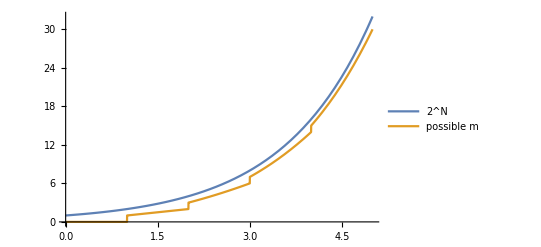

```mathematica
Plot[{2^N, Sum[Binomial[N,i],{i,1,Floor[N]}]},{N,0,5}, PlotLegends->{"2^N", "possible m"}]
```

```mathematica
a=Sum[Binomial[N,i],{i,1,Floor[N]}],{N,0,50}
```

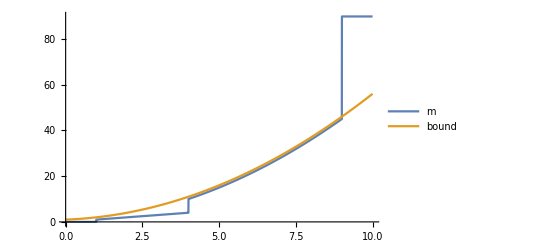

Set::write: Tag Sum in ∑_(i=1)^Floor[√N] Binomial[N,i] is Protected.

NSolve::fexp: Warning: NSolve used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

{{N→-1.},{N→-0.788331-1.25302 ⅈ},{N→-0.788331+1.25302 ⅈ},{N→-0.263263-2.64068 ⅈ},{N→-0.263263+2.64068 ⅈ},{N→0.483372-4.13802 ⅈ},{N→0.483372+4.13802 ⅈ},{N→1.4235-5.71386 ⅈ},{N→1.4235+5.71386 ⅈ},{N→2.54596-7.34687 ⅈ},{N→2.54596+7.34687 ⅈ},{N→3.84624-9.02078 ⅈ},{N→3.84624+9.02078 ⅈ},{N→5.3235-10.7219 ⅈ},{N→5.3235+10.7219 ⅈ},{N→6.97947-12.4382 ⅈ},{N→6.97947+12.4382 ⅈ},{N→8.81801-14.1579 ⅈ},{N→8.81801+14.1579 ⅈ},{N→10.845-15.8695 ⅈ},{N→10.845+15.8695 ⅈ},{N→13.0685-17.5611 ⅈ},{N→13.0685+17.5611 ⅈ},{N→15.4988-19.2196 ⅈ},{N→15.4988+19.2196 ⅈ},{N→18.1493-20.8306 ⅈ},{N→18.1493+20.8306 ⅈ},{N→21.0368-22.3773 ⅈ},{N→21.0368+22.3773 ⅈ},{N→24.1828-23.8395 ⅈ},{N→24.1828+23.8395 ⅈ},{N→27.6152-25.1928 ⅈ},{N→27.6152+25.1928 ⅈ},{N→31.3708-26.4056 ⅈ},{N→31.3708+26.4056 ⅈ},{N→35.4994-27.4366 ⅈ},{N→35.4994+27.4366 ⅈ},{N→40.0714-28.2293 ⅈ},{N→40.0714+28.2293 ⅈ},{N→45.1907-28.7022 ⅈ},{N→45.1907+28.7022 ⅈ},{N→51.0219-28.7306 ⅈ},{N→51.0219+28.7306 ⅈ},{N→57.8533-28.106 ⅈ},{N→57.8533+28.106 ⅈ},{N→66.2761-26.4278 ⅈ},{N→66.2761+26.4278 ⅈ},{N→77.9516-22.6899 ⅈ},{N→77.9516+22.6899 ⅈ}}

```mathematica
Plot[{Sum[Binomial[N,i],{i,1,Floor[Sqrt[N]]}],Sum[Binomial[N,i],{i,0,2}]},{N,0,10},PlotLegends->{"m","bound"}]
```

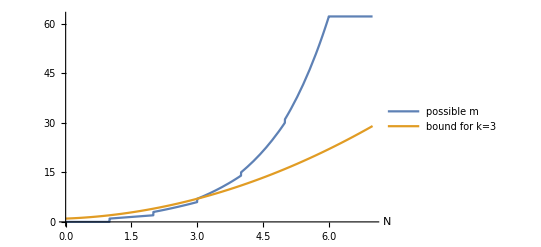

```mathematica
Plot[{Sum[Binomial[N,i],{i,1,Floor[N]}],Sum[Binomial[N,i],{i,0,2}]},{N,0,7},PlotLegends->{"possible m", "bound for k=3"},AxesLabel->{N}]
```

```mathematica
a = Expand[Simplify[1+(N+1)*N/2+Sum[Sum[Binomial[i-1,2]+Binomial[N+1-j,2],{i,1,j-1}],{j,1,N+1}]]]
```

```mathematica
1+(2 N)/3+(5 N^2)/12-N^3/6+N^4/12
```

```mathematica
a=Binomial[N+1,4]+Binomial[N+1,2]+1
```

1+1/2 N (1+N)+1/24 (-2+N) (-1+N) N (1+N)

```mathematica
Expand[Simplify[a]]
```

1+(7 N)/12+(11 N^2)/24-N^3/12+N^4/24

```mathematica
Expand[Simplify[Binomial[N+1,2]+Binomial[N+1,4]+1]]
```

1+(7 N)/12+(11 N^2)/24-N^3/12+N^4/24

```mathematica
Plot[Circle[{0,0},2]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[Circle[{0,0},2]]

```mathematica
1+Sum[Binomial[N+1,2i],{i,1,3}]
```

1+1/2 N (1+N)+1/24 (-2+N) (-1+N) N (1+N)+Binomial[1+N,6]

```mathematica
NSolve[Bin
```